```mathematica
imgSize=700;
```

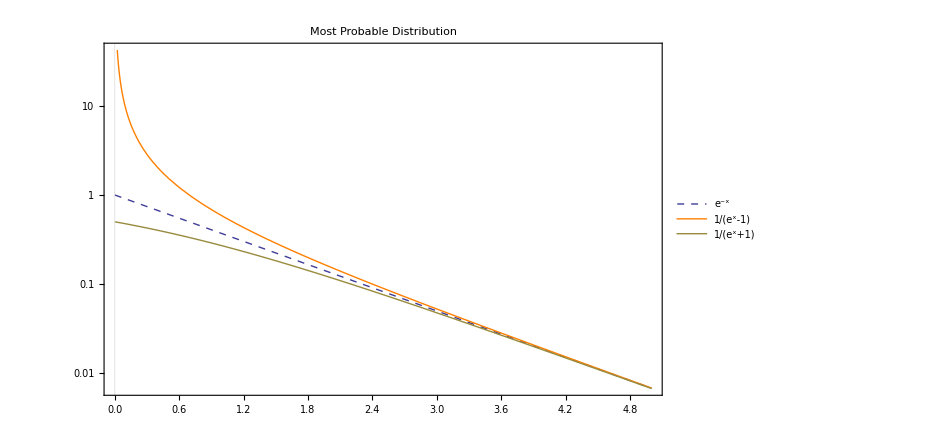

```mathematica
LogPlot[{Exp[-x],1/(Exp[x]-1),1/(Exp[x]+1)},{x,0,5},AxesOrigin->{0,0},PlotLegends->Placed[{Style["e^-x",Large],Style["1/(e^x-1)",Large],Style["1/(e^x+1)",Large]},Bottom],PlotStyle->{Dashed,Orange,Thick},PlotLabel->Style["Most Probable Distribution",Large],ImageSize->imgSize,Frame->True,GridLines->{{0},{}}]
```